# ACM 11 Ayaana Patel Sikora

## Problem 1: Mathematica as a Calculator

#### Question 1

```mathematica
valNum = 354224848179261915075;
IntegerQ[Sqrt[(5*(valNum^2))+4]] || IntegerQ[Sqrt[(5*(valNum^2))-4]]
```

True

This evaluates to True, thus indicating that the number 354,224,848,179,261,915,075 is in the fibonacci sequence.

#### Question 2

```mathematica
valNum2 = 2305843008138952128;
valNum2==(DivisorSigma[1,valNum2]) /2
```

False

This evaluates to False, thus indicating that the number 2,305,843,008,138,952,128 is not a perfect number (i.e. it is not equivalent to half the sum of all of its positive divisors).

#### Question 3

```mathematica
NextPrime[Prime[PrimePi[10^9]]]
```

1000000007

This shows that the smallest prime number above 1 billion is 1,000,000,007.

#### Question 4

```mathematica
SetPrecision[ZetaZero[20], 100]
```

0.5+77.14484006887480537268266485630463701579603244923446104176523145315113916425371508940828869469973776 ⅈ

Evaluating this gives the 20-th zero of the Riemann zeta function.

#### Question 5

```mathematica
Sum[((3^k)-1)/(4^k) * Zeta[k+1],{k, 1, Infinity}]
```

π

This computes the given sum to be Pi.

# Problem 2: High-Dimensional Balls and Monte Carlo

#### Part 1

```mathematica
Clear[n,R]
V[n_,R_]=((Pi^(n/2)) * (R^n))/Gamma[(n/2)+1]
S[n_, R_]=((n+1)*(Pi^((n+1)/2))*(R^n))/Gamma[(((n+1)/2) + 1)]
D[V[n,R],R] == S[(n-1), R]
```

(π^(n/2) R^n)/Gamma[1+n/2]

((1+n) π^((1+n)/2) R^n)/Gamma[1+(1+n)/2]

True

This creates the V(n, R) and S(n, R) functions and then confirms the given identity, S(n-1, R) = derivative of V(n, R) with respect to R.

#### Part 2

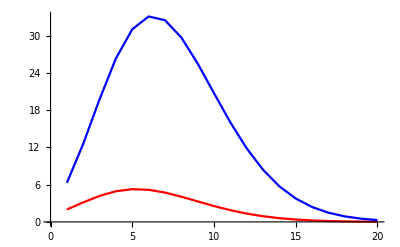

```mathematica
dataV = Table[{n, V[n,1]}, {n, 1, 20}];
dataS = Table[{n, S[n,1]}, {n,1,20}];
ListLinePlot[{dataV, dataS}, PlotStyle->{Red,Blue}]
```

#### Part 3

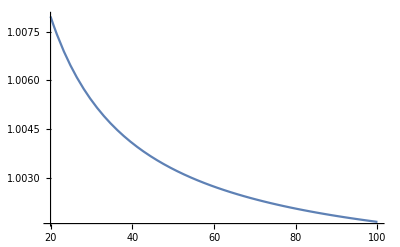

```mathematica
approxS[n_,R_]:=((n+1)*(Pi^((n+1)/2)) * (R^n))/(Sqrt[2*Pi]*Exp[(-(n+1))/2]*(((n+1)/2)^((n+2)/2)));
dataRatio = Plot[approxS[n,1]/S[n,1], {n, 20, 100}]
```

The limit of this ratio as n approaches infinity does not depend on R. This is because the only thing different between approxS and the S function is the denominator (the Gamma part), which does not depend on R. Thus, the R^n term in the numerator of both functions gets eliminated.

#### Part 4

```mathematica
n = 10;
m = 10^6;
points = RandomReal[{-1,1},{m, n}];
valPoints = Map[Norm, points];
numInRange = Count[valPoints,_?(#≤1&)];
currentVolume = N[((2^n) * numInRange)/10^6];
piApprox = (Gamma[(n/2)+1] *  currentVolume)^(2/n)
relativeError = Abs[Pi-piApprox]
```

3.13389

0.00770617

This approximates Pi using a sample size of 10^6 in a 10 dimensional space. This reports the approximation (~3.13363) and the relative error (0.00796099).

## Problem 3: Mandelbrot Set

#### Part 1

```mathematica
mandelbrot[cx_, cy_, nmax_]:= 
Module[{n = 0,zn = 0},
While[(n<nmax),
zn = (zn^2)+(cx+I*cy);
If[Norm[zn]≤ 2, n = n+1, Break[]]];
n
]
mandelbrot[1,0,100]
```

2

This creates the mandelbrot function and confirms that it works using an easily computable c value (it confirms that c = 1 gives m =2).

#### Part 2

```mathematica
Timing[mandelbrot[Sqrt[5]/100,0,1000]]
mandelbrotC=Compile[{cx, cy, nmax}, mandelbrot[cx, cy, nmax]]
```

{173.991,1000}

CompiledFunction[…]

```mathematica
Timing[mandelbrotC[Sqrt[5]/100,0,1000]]
```

{0.004639,1000.}

This runs the function on a more complicated c value, with a large nmax. I then created a compiled version of the mandelbrot and showed that the compiled version ran faster. To compare times, I used the Timing function. This showed that the uncompiled version took 0.49704 seconds while the comiled version took 0.004748 seconds.

#### Part 3

```mathematica
DensityPlot[-mandelbrotC[x,y,100],{x,-2,0.6},{y,-1.3,1.3},ColorFunction->GrayLevel, PlotPoints->100]
```

-Graphics-

#### Part 4

```mathematica
DensityPlot[-mandelbrotC[x,y,100],{x,-0.4,0.1},{y,0.6,1.1},ColorFunction->GrayLevel, PlotPoints->100]
```

-Graphics-

#### Part 5

```mathematica
DensityPlot[-mandelbrotC[x,y,1000],{x,-0.75,-0.747},{y,0.06,0.063},ColorFunction->GrayLevel, PlotPoints->300, ImageSize->Large]
```

-Graphics-